Hola Víctor. Cuidado a la notación r1=ρ_1^2 y r2=ρ_2^2

```mathematica
r1=y^2+(x-1)^2
r2=y^2+(x+1)^2
```

(-1+x)^2+y^2

(1+x)^2+y^2

Por lo tanto esta ecuación 2r1^2-(r1^2-2)^2-(r2^2-2)^2//Simplify debe ser

```mathematica
2r1-(r1-2)^2-(r2-2)^2//Simplify
```

-2 (2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4)

Observa que es de grado 4, como dice Schroeder

```mathematica
R=ImplicitRegion[2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4==0,{x,y}];
```

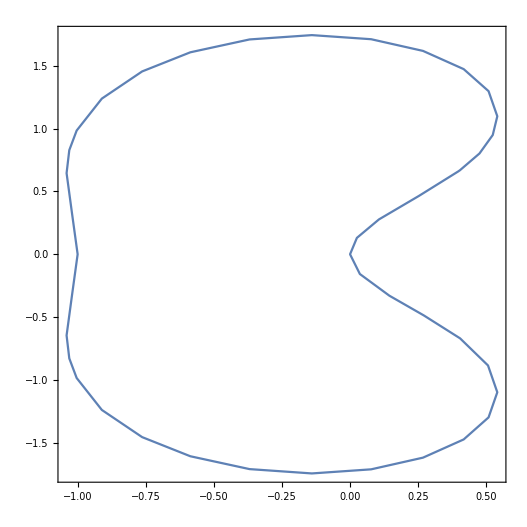

```mathematica
RegionPlot[R]
```

Algunos puntos de la curva y sus imágenes por el método de Schoeder:

```mathematica
f[z_]=(z-1)(z+1); Lf[z_]=f[z]f''[z]/f'[z]^2; sc[z_]=z-f[z]/f'[z]/(1-Lf[z])//Simplify
```

(2 z)/(1+z^2)

```mathematica
2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4/.x->0//Factor
```

y^2 (-3+y^2)

```mathematica
{sc[0],sc[Sqrt[3]I],sc[-Sqrt[3]I]}
```

{0,-ⅈ √3,ⅈ √3}

Los tres mantienen su distancia al 1

```mathematica
2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4/.y->0//Factor
```

x (1+x) (2-x+x^2)

```mathematica
NSolve[2-x+x^2==0,x,Reals]
```

{}

#### Por ejemplo, en la recta x=-1/2

```mathematica
2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4/.x->-1/2//Factor
```

1/16 (-11+4 y^2) (1+4 y^2)

```mathematica
{Abs[-1/2+Sqrt[11]/2I-1],Abs[sc[-1/2+Sqrt[11]/2I]-1]}
```

{√5,√5}

el punto y su imagen están a la misma distancia del 1

```mathematica
sc[-1/2+Sqrt[11]/2I]//ComplexExpand
```

-4/5-(2 ⅈ √11)/5

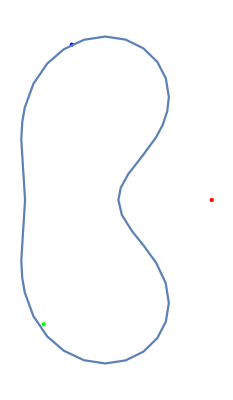

```mathematica
Show[Graphics[{PointSize[Large],Green,Point[{-4/5,-(2  √11)/5}]}],Graphics[{PointSize[Large],Blue,Point[{-1/2,(√11)/2}]}],Graphics[{PointSize[Large],Red,Point[{1,0}]}],RegionPlot[R]]
```

#### Por ejemplo, en la recta x=1/2

```mathematica
2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4/.x->1/2//Factor
```

1/16 (-7+4 y^2) (-3+4 y^2)

Hay cuatro puntos

```mathematica
{Abs[1/2+Sqrt[3]/2I-1],Abs[sc[1/2+Sqrt[3]/2I]-1]}
```

{1,1}

el punto y su imagen están a la misma distancia del 1

```mathematica
sc[1/2+Sqrt[3]/2I]//ComplexExpand
```

2

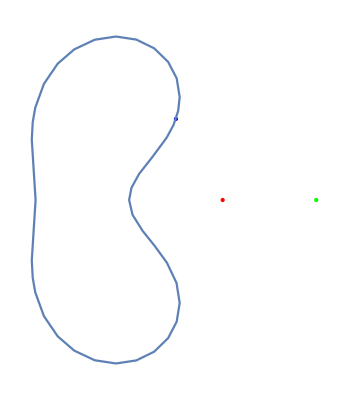

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{1/2,(√3)/2}]}],Graphics[{PointSize[Large],Green,Point[{2,0}]}],Graphics[{PointSize[Large],Red,Point[{1,0}]}],RegionPlot[R]]
```

Este otro punto también va al 2

```mathematica
sc[1/2-Sqrt[3]/2I]//ComplexExpand
```

2

Los otros dos:

```mathematica
{Abs[1/2+Sqrt[7]/2I],Abs[sc[1/2+Sqrt[7]/2I]-1]}
```

{√2,√2}

```mathematica
sc[1/2+Sqrt[7]/2I]//ComplexExpand
```

3/2-(ⅈ √7)/2

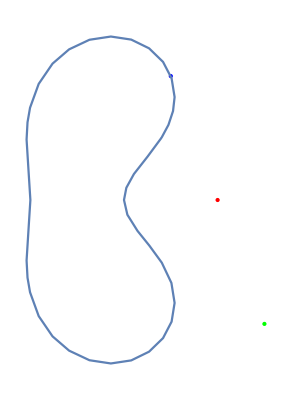

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{1/2,(√7)/2}]}],Graphics[{PointSize[Large],Green,Point[{3/2,(-√7)/2}]}],Graphics[{PointSize[Large],Red,Point[{1,0}]}],RegionPlot[R]]
```